```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/home/zack/oscillators/git/faraday

Single run plots

./faraday.py --geometry box --xmesh 8 --ymesh 3 --zmesh 5 --refinement 1 --width 1 --length 4 --height 2 --iamp 5e-3 --bmesh 0 --nonlinear 1 --time 200 --filebase data/boxsaturate4 --contact periodic --frequency 25 --acceleration 1.6

{4.,1.,2.}

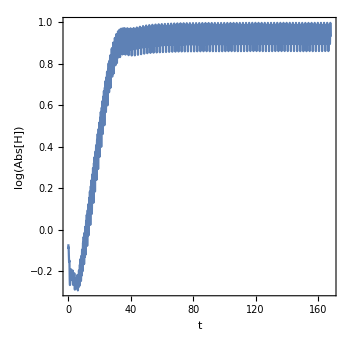
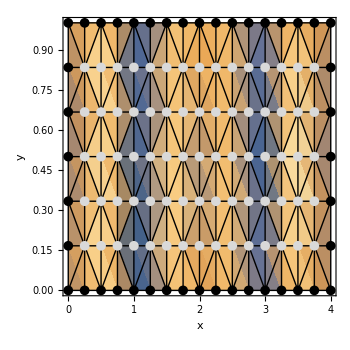
-Graphics- | -Graphics- | -Graphics3D-

```mathematica
filebase="data/boxsaturate4";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],3],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
steps=ToExpression[lst[[FirstPosition[lst,"Steps"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
width=ToExpression[lst[[FirstPosition[lst,"Width"][[1]]+1]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
lst[[1]]
{length,width,height}
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],4];
contop=Cases[con,u_/;Length[Intersection[top,u]]==3];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==3];
sides1=Flatten[Join[Position[mesh[[-1]],u_/;Length[u]>0&&u[[1]]==0],Position[mesh[[-1]],u_/;Length[u]>0&&u[[1]]==length]]];
sides2=Flatten[Join[Position[mesh[[-1]],u_/;Length[u]>0&&u[[2]]==0],Position[mesh[[-1]],u_/;Length[u]>0&&u[[2]]==width]]];
consides1=Cases[con,u_/;Length[Intersection[sides1,u]]≥3];
consides2=Cases[con,u_/;Length[Intersection[sides2,u]]≥3];
m=Length[mesh]-5;
mesh2=mesh[[m]];
p=Grid[{{ListPlot[Transpose[{Range[m]/steps,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListDensityPlot[mesh2[[top]],PlotRange->All,InterpolationOrder->10,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,y},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Graphics[Line[{mesh2[[#[[1]],{1,2}]],mesh2[[#[[2]],{1,2}]]}]&/@DeleteDuplicates[Flatten[Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),1]]],ListPlot[{mesh2[[Complement[top,top2],{1,2}]],mesh2[[top2,{1,2}]]},PlotStyle->{Directive[Black,PointSize[0.02]],Directive[LightGray,PointSize[0.02]]}]],Show[Graphics3D[{Sphere[#,0.025]&/@mesh2[[top]],Sphere[#,0.025]&/@mesh2[[bottom]],Sphere[#,0.025]&/@mesh2[[sides1]],Sphere[#,0.025]&/@mesh2[[sides2]],Opacity[0.5],EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Blue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides1]&/@consides1),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides2]&/@consides2),Thickness[0.001],Opacity[0.5],Line[{mesh2[[#[[1]]]],mesh2[[#[[2]]]]}]&/@Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),Line[{mesh2[[#[[1]]]],mesh2[[#[[2]]]]}]&/@Subsets[#,{2}]&/@(Intersection[#,bottom]&/@conbottom)},Boxed->False,ImageSize->500,PlotRange->{All,All,{Min[mesh[[All,All,3]]]-1,Max[mesh[[All,All,3]]]+1}}],
Show[ListPlot3D[mesh2[[bottom]],PlotRange->{All,All,{Min[mesh[[All,All,3]]]-1,Max[mesh[[All,All,3]]]+1}},Boxed->False,AspectRatio->1,Mesh->None,Axes->False,ImageSize->500,PlotStyle->Opacity[0.5]],ListPlot3D[mesh2[[top]],PlotRange->{All,All,{Min[mesh[[All,All,3]]],Max[mesh[[All,All,3]]]}},Boxed->False,AspectRatio->1,Mesh->None,Axes->False,ImageSize->500,PlotStyle->Directive[Opacity[0.5],Blue]]],ViewPoint->{0, -3, 1}]}}]
```

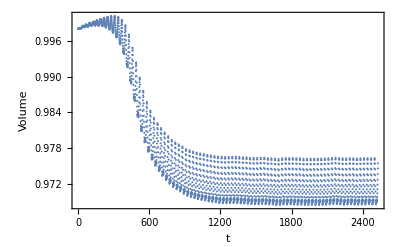

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,3]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

```mathematica
modes=Sort[Flatten[Table[((n1*Pi/width)^2+(n2*Pi/length)^2)^(1/2),{n1,0,5},{n2,0,5}]]]
frequencies=2*(980*#*Tanh[height*#]*(1+72/980*#^2))^(1/2)/(2*Pi)&/@modes
modes2=SortBy[Flatten[Table[{#,(980*#*Tanh[height*#]*(1+72/980*#^2))^(1/2)/(2*Pi),{n1,n2}}&@(((n1*Pi/width)^2+(n2*Pi/length)^2)^(1/2)),{n1,0,5},{n2,0,5}],1],First]
```

{0.,0.785398,1.5708,2.35619,3.14159,3.14159,3.23828,3.51241,3.92699,3.92699,4.44288,5.029,6.28319,6.33208,6.47656,6.71044,7.02481,7.40943,9.42478,9.45745,9.55478,9.71484,9.93459,10.2102,12.5664,12.5909,12.6642,12.7854,12.9531,13.1657,15.708,15.7276,15.7863,15.8837,16.019,16.1914}

{0.,8.64676,13.5484,18.1475,23.1977,23.1977,23.8594,25.7853,28.8395,28.8395,32.8775,37.7784,49.33,49.8084,51.2339,53.5788,56.8019,60.8539,83.9231,84.3212,85.5115,87.4831,90.2184,93.6945,125.396,125.744,126.785,128.515,130.923,133.997,172.725,173.038,173.974,175.531,177.703,180.482}

{{0.,0.,{0,0}},{0.785398,4.32338,{0,1}},{1.5708,6.7742,{0,2}},{2.35619,9.07373,{0,3}},{3.14159,11.5989,{0,4}},{3.14159,11.5989,{1,0}},{3.23828,11.9297,{1,1}},{3.51241,12.8926,{1,2}},{3.92699,14.4197,{0,5}},{3.92699,14.4197,{1,3}},{4.44288,16.4388,{1,4}},{5.029,18.8892,{1,5}},{6.28319,24.665,{2,0}},{6.33208,24.9042,{2,1}},{6.47656,25.617,{2,2}},{6.71044,26.7894,{2,3}},{7.02481,28.401,{2,4}},{7.40943,30.4269,{2,5}},{9.42478,41.9616,{3,0}},{9.45745,42.1606,{3,1}},{9.55478,42.7558,{3,2}},{9.71484,43.7416,{3,3}},{9.93459,45.1092,{3,4}},{10.2102,46.8472,{3,5}},{12.5664,62.6982,{4,0}},{12.5909,62.872,{4,1}},{12.6642,63.3927,{4,2}},{12.7854,64.2574,{4,3}},{12.9531,65.4614,{4,4}},{13.1657,66.9986,{4,5}},{15.708,86.3627,{5,0}},{15.7276,86.5189,{5,1}},{15.7863,86.9871,{5,2}},{15.8837,87.7655,{5,3}},{16.019,88.8514,{5,4}},{16.1914,90.241,{5,5}}}

Animation

```mathematica
m0=Length[mesh]-750;
m1=Length[mesh];
If[!DirectoryQ["boxanimation"],CreateDirectory["boxanimation"]]
Monitor[Do[
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
mesh2={#[[1]],#[[2]],z0+#[[3]]}&/@mesh[[m]];
p=Grid[{{ListPlot[{Transpose[{Range[Length[norms]]/15,Log[norms]/Log[10]}],Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}]},Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->{Directive[LightGray,AbsoluteThickness[1]],Directive[Black,AbsoluteThickness[2]]},FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListDensityPlot[mesh[[m,top]],PlotRange->All,InterpolationOrder->10,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,y},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Graphics[Line[{mesh[[m,#[[1]],{1,2}]],mesh[[m,#[[2]],{1,2}]]}]&/@DeleteDuplicates[Flatten[Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),1]]],ListPlot[{mesh[[m,Complement[top,top2],{1,2}]],mesh[[m,top2,{1,2}]]},PlotStyle->{Directive[Black,PointSize[0.02]],Directive[LightGray,PointSize[0.02]]}]],Show[Graphics3D[{Sphere[#,0.05]&/@mesh2[[top]],Sphere[#,0.05]&/@mesh2[[bottom]],Sphere[#,0.05]&/@mesh2[[sides]],Opacity[0.5],EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Blue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides]&/@consides),Thickness[0.001],Opacity[0.5],Line[{mesh2[[#[[1]]]],mesh2[[#[[2]]]]}]&/@Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),Line[{mesh2[[#[[1]]]],mesh2[[#[[2]]]]}]&/@Subsets[#,{2}]&/@(Intersection[#,bottom]&/@conbottom)},Boxed->False,ImageSize->500,PlotRange->{All,All,{-1,height+1}}],Show[ListPlot3D[mesh2[[bottom]],PlotRange->{All,All,{-1,height+1}},Boxed->False,AspectRatio->1,Mesh->None,Axes->False,ImageSize->500,PlotStyle->Opacity[0.5]],ListPlot3D[mesh2[[top]],PlotRange->{All,All,{-1,height+1}},Boxed->False,AspectRatio->1,Mesh->None,Axes->False,ImageSize->500,PlotStyle->Directive[Opacity[0.5],Blue]]],ViewPoint->{0, -3, 1}]}}];
Export["animation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

```mathematica
Do[Export[filebase<>"/params"<>ToString[i]<>".txt", Partition[DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],2][[1;;-1,2]]],{i,1,50}]
```

Sweep plots

sb1

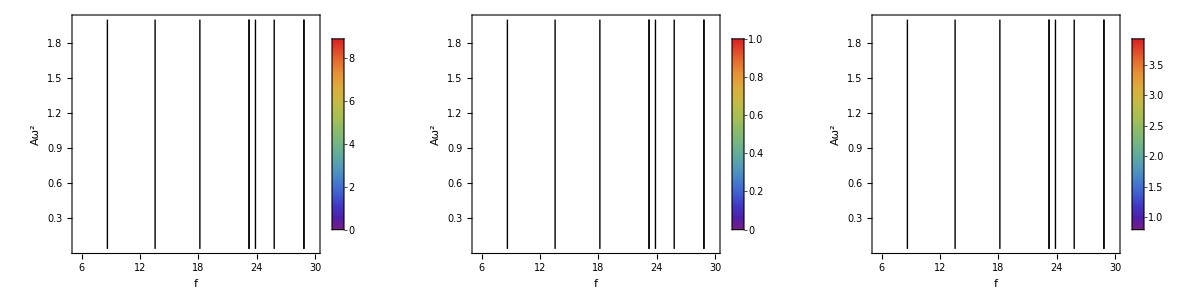

```mathematica
filebase="sb1"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,50}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=Min[growth1[[All,5]]];
kmax=Max[growth1[[All,5]]];
max=Max[growth1[[All,4]]];
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,max}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.9*kmin,1.1*kmax}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

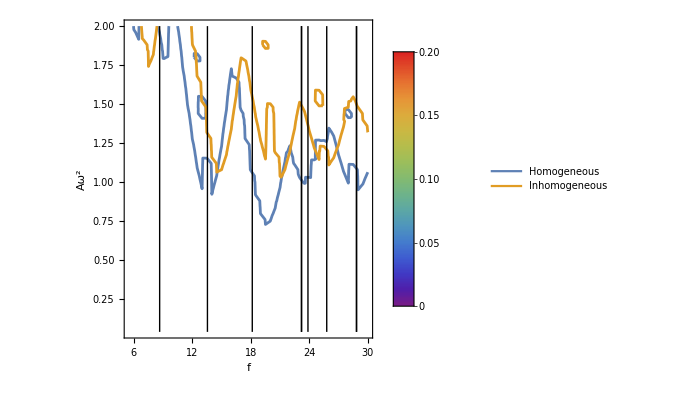

```mathematica
filebase="sb2";
growth2=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,50}],1];
sweeps={growth1,growth2};
p=Show@@Table[ListContourPlot[sweeps[[i,All,{1,2,4}]],Contours->{0.0},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,None}},Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],AbsoluteThickness[1],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax],Dashed,Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]}],{i,1,Length[sweeps]}];
Legended[p,LineLegend[ColorData[97,"ColorList"],{"Homogeneous","Inhomogeneous"}]]
```

Flat substrate Floquet predictions

```mathematica
rate[k_,ω_,A_,σ_,ν_]:=Module[{t0,t1,sol,norms,maxes},
t0=2*Pi*25;
t1=2*Pi*50;
sol=First@NDSolve[{ω^2*h''[t]==k*Tanh[k]*((-1+A*ω*Sin[t]-σ*k^2)*h[t]-ν*ω*h'[t]), h[0]==0.001, h'[0]==0}, h[t], {t,0,t1}];
norms=Table[h[t]/.sol,{t,t0,t1,2*Pi*0.1}];
maxes=First/@Position[Differences[Sign[Differences[norms]]],-2];
If[Mean[Log[Abs[norms]]]/Log[10]<-5,{k,ω,A,1/(0.1*Mean[Differences[maxes]]),-1,norms},{k,ω,A,1/(0.1*Mean[Differences[maxes]]),D[ω*Fit[Transpose[{2*Pi*0.1*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x],norms}]]
ωmin=1.5;
ωmax=4.0;
Amin=0.0;
Amax=0.3;
ν=0.05;
σ=0.1;
M=50;
AbsoluteTiming[Monitor[rates=Flatten[Table[First@MaximalBy[Table[rate[k,ω,A,σ,ν][[1;;5]],{k,modes}],#[[5]]&],{ω,ωmin,ωmax,(ωmax-ωmin)/M},{A,Amin,Amax,(Amax-Amin)/M}],1];,N[{(ω-ωmin)/(ωmax-ωmin),(A-Amin)/(Amax-Amin)}]]]
```

```mathematica
p2=Grid[{{rasterizeBackground[Show[ListDensityPlot[rates[[All,{2,3,5}]],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],PlotRange->{0,0.2},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/0.2]&), FrameLabel->{{A,None},{ω,"Growth Rate"}},ClippingStyle->None],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes]*(1+σ*modes^2))^(1/2)),u_/;u<4]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,4}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/1]&),PlotRange->{0,1.1},ClippingStyle->None, FrameLabel->{{A,None},{ω,"Frequency"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes]*(1+σ*modes^2))^(1/2)),u_/;u<4]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,1}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][(#-1)/2]&),PlotRange->{0.9,3.1}, ClippingStyle->None,FrameLabel->{{A,None},{ω,"Wave Number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{1,3}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes]*(1+σ*modes^2))^(1/2)),u_/;u<4]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```